# Reference

```mathematica
dsptdef[]:=(Global`INIT=True;
Global`Normalise=Normalize;
Global`e=E;
Global`i=I;
Global`dsptdeva::usage="dsptdeva[f[x], bool derivative, str domain, x*]\n domain like \"(a,b)\", \"[a,b]\", etc]\nPlots function, optional derivative, asymptotes, critical points.";
Global`dsptdeva[equ_,derl_,dom_,x_:x]:=Module[{der,domparts,domrem,compequ,points,asy,asym,xvals,xint,tp},domrem=StringTrim[dom,{"[","]","(",")"}];
domrem=StringSplit[domrem,","];
domparts={StringTake[dom,1],ToExpression[domrem[[1]]],ToExpression[domrem[[2]]],StringTake[dom,-1]};
If[derl,compequ={equ,D[equ,x]},compequ=equ];
asy=x/. Solve[Denominator[equ]==0,x];(*vertical asymptote*)asym=Limit[equ,x->Infinity];(*horizontal asymptote*)xvals={0};
xint=x/. Solve[equ==0&&domparts[[2]]<=x<=domparts[[3]],x];
xvals=Join[xvals,xint];
tp=x/. Solve[D[equ,x]==0&&domparts[[2]]<=x<=domparts[[3]],x];
xvals=Union[Join[xvals,tp]];
points=Labeled[{#,equ/. x->#},"("<>ToString[#]<>","<>ToString[equ/. x->#]<>")"]&/@xvals;
Show[Plot[{compequ},{x,domparts[[2]],domparts[[3]]},PlotRange->Automatic],ListPlot[points,AspectRatio->1],ContourPlot[x==asy,{x,domparts[[2]],domparts[[3]]},{y,-10,10},ContourStyle->{Black,Dashed}],Plot[{asym},{x,domparts[[2]],domparts[[3]]},PlotStyle->{Black,Dashed}]]];
Global`dsptbisec::usage="dsptbisec[f[x], a, b, iterations, x*]\nFinds root using the bisection method.";
Global`dsptbisec[equ_,ain_,bin_,nit_,x_:x]:=Module[{f,a,b,xo},f=(equ/. x->#&);
a={ain};b={bin};xo={};
If[Sign[f[a[[1]]]]*Sign[f[b[[1]]]]<0,Print[Style["All OK, execute the algorithm.",Blue]],Print[Style["f(a) and f(b) do not have opposite signs. Choose different values of a and b.",14,Red]]];
Do[xo=Append[xo,(a[[n]]+b[[n]])/2];
If[f[xo[[n]]]*f[b[[n]]]<0,a=Append[a,xo[[n]]];b=Append[b,b[[n]]],a=Append[a,a[[n]]];b=Append[b,xo[[n]]]],{n,nit}];
Print[Style[Row[{"Approximate solution to ",f[x]//TraditionalForm," = 0 after ",nit," iterations is ",N[xo[[nit]],6]}],FontColor->Blue]];
Print[Table[{n,xo[[n]]},{n,1,nit}]//TableForm//N];];
Global`dsptnewt::usage="dsptnewt[f[x], initial, iterations, x*]\nNewton-Raphson method for root finding.";
Global`dsptnewt[equ_,ini_,nit_,x_:x]:=Module[{f,o,dist1},f=(equ/. x->#&);
o[0]:=ini;
Do[o[n+1]=o[n]-(f[o[n]])/(D[f[x],x]/. x->o[n]),{n,0,nit}];
Print[Style[Row[{"Approximate solution to ",f[x]," = 0 after ",nit," iterations is ",N[o[nit],5]}],FontColor->Blue]];
dist1=Table[{n,o[n],o[n]-o[n-1],f[o[n]]},{n,1,nit}]//N;
Print[Grid[Prepend[dist1,{"Iteration","Approximate solution","Difference","f(x)"}]]];];
Global`dsptmdr::usage="dsptmdr[f[x],x*,y*]\nPrint domain and range of a function (may be unreliable).";
Global`dsptmdr[equ_,x_:x,y_:y]:=Module[{},Print["Domain: ",FunctionDomain[equ,x]];
Print["Range: ",FunctionRange[equ,x,y]];];
Global`dsptf::usage="dsptf[f[x],x*,y*]\nreturns traditional form without the font dying.";
Global`dsptf[equ_]:=Module[{},Return[Defer[TraditionalForm[equ]]];];
Global`dsptcompsq::usage ="compsq[f[x],x(optional)]\ncompletes square for f[x] using x as the variable";
Global`dsptcompsq[equ_,x_:x]:=Module[{a,b,c},a=Coefficient[equ,x,2];
b=Coefficient[equ,x,1];
c=Coefficient[equ,x,0];
Return[dsptf[a (x+b/(2 a))^2+c-b^2/(4 a)]];];
Global`dsptavg::usage = "dsptavg[f[x],a,b,x*]\nfinds the average value of the integral between a and b. swapping a and b swaps the sign.";
Global`dsptavg[equ_,a_,b_,x_:x]:=Module[{},
period=RealAbs[b-a];
int=Integrate[equ,{x,a,b}];
Return[int/period];
];
Global`dspttrap::usage="dspttrap[f[x],a,b,number]\nPrints the approximate area of f[x] between a and b using number trapeziums";Global`dspttrap[equ_,ain_,bin_,number_,x_:x]:=Module[{f,a,b,num},f:=(equ/. x->#&);
a=ain;b=bin;num=number;
h=(b-a)/num;
area=1/2 h (f[a]+f[b]+2 Sum[f[a+its*h],{its,1,num-1}]);
Print[area]];
Global`solveprobdist::usage="solveprobdist[inarr,k*]\nTakes a 1D array of functions of k. Solves for the values of k that make the output of all functions sum to 1, rejecting results that have any one of the functions outside the interval [0,1].";
Global`solveprobdist[inarr_,x_:k]:=Module[{},
sum=Total[inarr];
Solve[sum==1,x];
solns=x/.Solve[sum==1,x];
Print[solns];
numparts=Length[inarr];
numsols=Length[solns];
For[iit=1,iit<=numparts,iit++,
tmpfnc=inarr[[iit]];
For[jit=1,jit<=numsols,jit++,
tmpans=tmpfnc/.x->solns[[jit]];
If[Not[0<=tmpans<=1],
solns[[jit]]=Null;
];
];
];
outsolns={};
For[jit=1,jit<=numsols,jit++,
If[Not[solns[[jit]]===Null],
AppendTo[outsolns,solns[[jit]]];
];
];
Return[outsolns]
];
Global`array::usage="\!\(\*RowBox[{\"array\", \"[\", 
  RowBox[{StyleBox[\"{x1, x2, …, xn}\", \"TI\"], \",\", 
  StyleBox[\"initval*\", \"TI\"]}], \"]\"}]\)\nPrints an \!\(\*StyleBox[\"n\", \"TI\"]\)-dimensional array of size \!\(\*RowBox[{StyleBox[\"x1\", \"TI\"], \"*\", 
  StyleBox[\"x2\", \"TI\"], \"*\", \"…\", \"*\", 
  StyleBox[\"xn\", \"TI\"]}]\), with all elements initialised to \!\(\*StyleBox[\"initval\", \"TI\"]\).\n\!\(\*StyleBox[\"initval\", \"TI\"]\) defaults to 0 if no argument is given.\n\!\(\*StyleBox[\"Created by Pepper Scott :3\", FontSize -> 10]\)";
Global`array[x_,initval_:0]:=Module[{},
initfunc[__]:=initval;
Return[Array[initfunc,x]//MatrixForm];
];
Global`simplearray::usage="\!\(\*RowBox[{\"simplearray\", \"[\", 
  RowBox[{StyleBox[\"{x1, x2, …, xn}\", \"TI\"], \",\", 
  StyleBox[\"initval*\", \"TI\"]}], \"]\"}]\)\nReturns an \!\(\*StyleBox[\"n\", \"TI\"]\)-dimensional array of size \!\(\*RowBox[{StyleBox[\"x1\", \"TI\"], \"*\", 
  StyleBox[\"x2\", \"TI\"], \"*\", \"…\", \"*\", 
  StyleBox[\"xn\", \"TI\"]}]\), with all elements initialised to \!\(\*StyleBox[\"initval\", \"TI\"]\).\n\!\(\*StyleBox[\"initval\", \"TI\"]\) defaults to 0 if no argument is given.\n\!\(\*StyleBox[\"Created by Pepper Scott :3\", FontSize -> 10]\)";
Global`simplearray[x_,initval_:0]:=Module[{},
initfunc[__]:=initval;
Return[Array[initfunc,x]];
];
Global`rr::usage="rr[matrix]\nRow reduces a matrix and prints it in matrix form";
Gloabl`rr[mat_]:=Module[{},Return[MatrixForm[RowReduce[mat]]]];
Global`dsptca::usage="dsptca\nnukes all variables";
Global`dsptca:=Module[{},With[{syms=Select[Names["Global`*"],#=!="dsptdef"&]},ClearAll@@syms];
dsptdef[];];);
dsptdef[];
```

## Basics

### Add

```mathematica
5+8(*press shift+return*)
```

13

### Subtract

```mathematica
13-5
```

8

### Multiply

```mathematica
5*8
```

40

### Divide

```mathematica
40/8
```

5

### Exponent

```mathematica
2^3 or 3^5 (*ctrl + 6*)
```

8

### Root

```mathematica
8^(1/3)(*ctrl+2 for √□, ctrl+2 -> ctrl+5 for □^(1/□)*)
```

2

### Store var

```mathematica
x+10/.x->4(*- > makes ->*)
```

14

```mathematica
x=5
```

5

```mathematica
2x
```

10

```mathematica
2xy+3yx
```

2 xy+3 yx

```mathematica
2 x y+3 y x
```

5 x y

```mathematica
Clear[x]
```

### Suppress output

```mathematica
2+5;
```

```mathematica
a=2;
```

### Solve

```mathematica
Solve[2a+1==5]
```

{{a→2}}

```mathematica
Solve[{y==x+2,y==2x-1},{x,y}]
```

{{x→3,y→5}}

### Simplify

```mathematica
Simplify[2/(4x)+3/(8x)]
```

7/(8 x)

```mathematica
3(x-2)+3x+1/2(x+2)^2//Simplify
```

-4+8 x+x^2/2

```mathematica
3(x-2)+3x+1/2(x+2)^2//FullSimplify
```

-4+1/2 x (16+x)

```mathematica
Expand((x+4)(x-2))//TraditionalForm
```

Expand (x-2) (x+4)

```mathematica
3/4*5/8
```

15/32

```mathematica
3/4*5/8//N
```

0.46875

```mathematica
628/3(*use 'numerical value' on suggestion bar*)
```

628/3

```mathematica
N[628/3]
```

209.333

### Line segment

```mathematica
EuclideanDistance[{1,2},{3,4}]
```

2 √2

```mathematica
Midpoint[{{1,2},{3,4}}]
```

{2,3}

### Define

```mathematica
f[x_]:=2x-3
```

```mathematica
f[9]
```

15

### Freeform

WolframAlphaQueryParseResults

-Graphics3D-

WolframAlphaQueryParseResults

-Graphics-

### Matrix

```mathematica
mat1={{1,3,-2},{2,5,0},{-3,-5,7}};
```

```mathematica
Det[mat1]
```

-17

#### Clear

```mathematica
Clear["Global`*"]
```

```mathematica
ClearAll["Global`*"]
```

## Quadratics

### Quadratic formula

```mathematica
quad[a_,b_,c_]:=(-b±√(b^2-4a c))/(2a)//TraditionalForm
```

```mathematica
quad[2,4,-3]
```

1/4 (-4±2 √10)

### TP form

```mathematica
compsq[a_,b_,c_]:=a(x+b/(2 a))^2-(b^2-4a c)/(4a)//TraditionalForm (*copy-paste into exam and enter a, b and c*)
```

```mathematica
compsq[4,10,7]
```

4 (x+5/4)^2+3/4

```mathematica
∑_(n=0)^∞ 1/(n!)
```

ⅇ

```mathematica
N[ⅇ]
```

2.71828

```mathematica
SolveAlways[6 x^3-7 x^2-x+2==(x-1)(a,b,c),x]
```

## Probability

### Rules

```mathematica
Pr(A ∪ B) = Pr(A) + Pr(B) - Pr(A ∩ B) 

Inderpendent if Pr(A∩B) = Pr(A)*Pr(B)

Pr(A\B) = (Pr(A∩B))/(Pr(B))

Pr(B\A) = (Pr(A∩B))/(Pr(A))
```

### Binomial dist

```mathematica
(*
Expected vaue = n*p
Variance = n*p*q=n*p*(1-p)
Standard deviation=√Variance=√(n*p*q)=√(n*p*(1-p))
where
n=# trials
p=probability(success)
q=probability(failure)=(1-p)
*)
```

```mathematica
Variance: E(x^2)-E(x)^2
```

```mathematica
-Graphics--Graphics--Graphics-
```

```mathematica
-Graphics--Graphics--Graphics-
```

## Glossary

### Probability

```mathematica
(*
Trial is one try of a random event


*)
```

## Graphing

### Plot

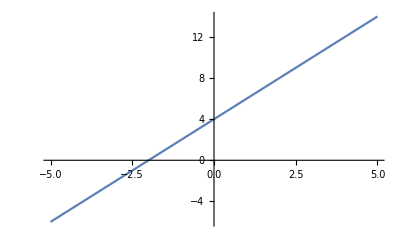

```mathematica
Plot[2x+4,{x,-5,5}]
```

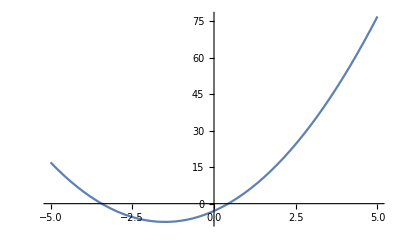

```mathematica
Plot[2 x^2+6x-3,{x,-5,5}]
```

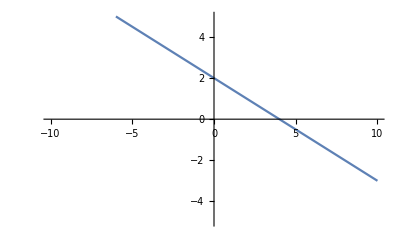

```mathematica
Plot[-x/2+2,{x,-10,10},PlotRange->{-5,5}]
```

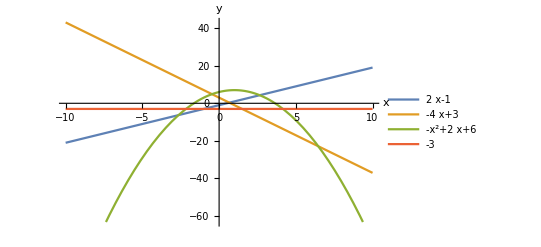

```mathematica
Plot[{2x-1,-4x+3,-x^2+2x+6,-3},{x,-10,10},PlotLegends->"Expressions",AxesLabel->{"x","y"}]
```

### Plot true shape

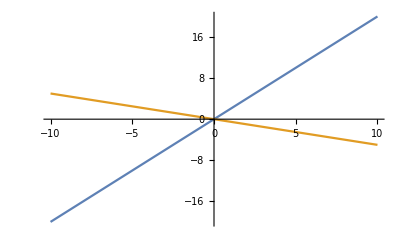

```mathematica
Plot[{2x,-1/2 x},{x,-10,10}]
```

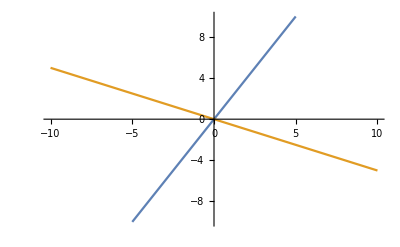

```mathematica
Plot[{2x,-1/2 x},{x,-10,10},PlotRange->{-10,10}]
```

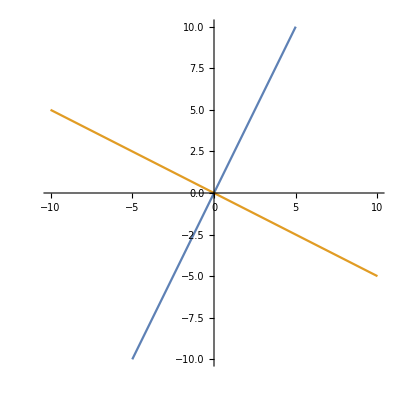

```mathematica
Plot[{2x,-1/2 x},{x,-10,10},PlotRange->{-10,10},AspectRatio->1]
```

### Exponentials

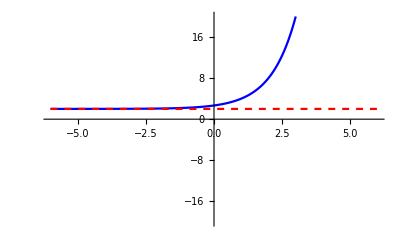

```mathematica
Plot[{2*3^(x-1)+2,2},{x,-6,6},PlotRange->{-20,20}, PlotStyle->{Blue,{Red,Dashed}}]
```

## Trig

### SohCahToa

```mathematica
Cos[24°]//N
```

0.913545

```mathematica
Cos[24 Degree]//N
```

0.913545

### Find angle

```mathematica
ArcSin[2/6]/Degree//N
```

19.4712

## Vectors

### Planes

## Sequences and series

### Arithmetic

```mathematica
t[n]=a t[n-1]+b
t[n]=a+(n-1)d
S [n] =n/2(2a+(n-1)d)
```

### Geometric

```mathematica
t[n]=t[n-1] r
t[n]=ar^(n-1)
t[n]=ar+ar^2+ar^3+...+ar^(n-1)+ar^n
S[n]=a(r^n-1)/(r-1)
```

## Modulus/Abs/Piecewise

### Modulus

```mathematica
a
```

### Abs

```mathematica
Abs[x-4]==6//Solve
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-2},{x→10}}

### Piecewise

```mathematica
f[x_]:=RealAbs[x-4]
```

```mathematica
PiecewiseExpand[f[x]]
```

Piecewise[{{4-x, x<4}, {-4+x, True}}]

## Unimportant

### Image

WolframAlphaQueryParseResults

-Graphics-

```mathematica
FacialFeatures[%]
```

{<|Image→-Graphics-,Age→37,Gender→Male,Emotion→neutral|>}

### Funny

WolframAlphaQueryResults

```mathematica
[π,{1,100}]//N
```

WolframAlphaQueryResults

(SlowLarge)

### Animations

```mathematica
Manipulate[Plot[Sin[freq x]/x^2,{x,-10,10},PlotRange->4],{freq,1,5}]
```

```mathematica
Manipulate[Plot[amp Sin[freq x]/x,{x,-10,10},PlotRange->4],{freq,1,5}, {amp, 1, 4}]
```

```mathematica
Manipulate[Plot[amp func[freq x]/x,{x,-10,10},PlotRange->4],{freq,1,5}, {amp, 1, 4},{func,{Sin, Cos, Tan}}]
```

## Symbols

### ^ (ctrl)

```mathematica
√□^ + 2
```

```mathematica
□^□ ^ + 6
```

□^(6 □)

```mathematica
□/□^+/
```

1

### (esc)

```mathematica
deg  esc + 'deg' + esc ( ° )
 un  (∪)
 inter  (∩)
```

```mathematica
Abs[√2(Cos[π/4]+ⅈ Sin[π/4])]
```

√2

```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```